# Figures 2C(bottom), 2D(right),2E(right),2F(right) 3B(middle), 4B

### This notebook generates the above figure panels . It used pre-processed data generated by process_ODs.nb

## Helper functions

```mathematica
SetDirectory[NotebookDirectory[]]

ksround=0.01; (* round-off parameters for the KS test for the least-frequent strain data *)

SE[x_]:=If[Length[x]>1,Sqrt[Variance[x]/Length[x]],0]
Clear[DispPval]
DispPval[p_]:=Which[p<0.001,"<0.001",p<0.01,ToString[NumberForm[p,{2,4}]],p<0.1,ToString[NumberForm[p,{2,3}]],p<1,ToString[NumberForm[p,{2,2}]],p==1,"p=1.0"]

SetOptions[{ListPlot,ListLogPlot,ListLinePlot,Histogram,BarChart,Graphics},BaseStyle->FontSize->24,Frame->True,FrameStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}},AxesStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}}];

Clear[NaiveMinimization]
NaiveMinimization[fun_,a0_,b0_,ϵ_]:=Module[{a,b,c,d,fa,fb,fc,fd,gr=1.(Sqrt[5]+1)/2},a=1.a0;b=1.b0;Do[
c=b-(b-a)/gr;
d=a+(b-a)/gr;
fa=fun[a];fb=fun[b];fc=fun[c];fd=fun[d];
If[fc<fd,b=d;fb=fd,a=c;fa=fc];
Print[a," ",b, " fa=",fc," fb=",fb];
If[(b-a)<ϵ,Break[]]
,{n,10}];
Return[(a+b)/2]]

Clear[FisherExactTest]
FisherExactTest[succ1_,n1_,succ2_,n2_]:=1.(n1! n2! (n1+n2-succ1-succ2)! (succ1+succ2)!)/((n1+n2)! (n1-succ1)! succ1! (n2-succ2)! succ2!)
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor

## Data import and model parameters:

```mathematica
<<("turb_str_long_runs_ODvsTIME.mx");
dataSTRlong=data;
Length[dataSTRlong]

<<("turb_str_long_runs.mx");
paramsSTRlong=alldata;

<<("turb_str_short_runs.mx")
paramsSTRshort=alldata;
Print[Length[paramsSTRshort[[1]]]]

experfractions=Select[{0,n,n,n,0,n,n,0,n,n,n,n,n,n,n,n,n,n,n,n,n,n,n,n}/.n->"n" (* n = no regrowth *),(NumberQ[#])&];
cfus={1,0,0,0,  0,0,0,1,  1,0,0,0}; (* only large colonies *)
cfusall={21,22,11,7, 21,21,8,44, 9,50,18,13} ;(* all colonies but we exclude these ones:  284,466,256,153 because the numbers look like it might have been a pre-existing mutation *)

tmax=30;odcrit=0.1;
odregrowth=0.05;dilf=0.75;


(* for plotting and simulations *)
tregrowthbin={10,26,2};
tregrowthpmax=0.25;
cfubindata={10,1,0.8};
cfuallbindata={80,2,0.16};
noreps="1000" ;(* number of replicate simulations *)
```

24

16

## Plotting functions

```mathematica
Clear[MakeBar2,MakeBarFromNM,RegrowthProbPlot,RegrowtTimeDistribution,LeastAbundantStrain]
MakeBar2[x_,y1_,y2_]:={AbsolutePointSize[10],Point[{x,(y1+y2)/2}],AbsoluteThickness[2],Line[{{x-0.25,y1},{x+0.25,y1}}],Line[{{x-0.25,y2},{x+0.25,y2}}],AbsoluteThickness[1],Line[{{x-0.15,y1},{x+0.15,y1}}],Line[{{x-0.15,y2},{x+0.15,y2}}],Line[{{x,y1},{x,y2}}]};
MakeBarFromNM[x_,n_,m_]:=MakeBar2[x,(m+1/2z^2)/(n+z^2)-z/(n+z^2)Sqrt[m (n-m)/n+z^2/4],(m+1/2z^2)/(n+z^2)+z/(n+z^2)Sqrt[m (n-m)/n+z^2/4]]/.z->1 (* Wilson score interval https://en.wikipedia.org/wiki/Binomial_proportion_confidence_interval *)
RegrowthProbPlot[name_]:=Module[{gr,pval,pexp,pth,muypos},
pval=FisherExactTest[Length[Select[tmp,NumberQ[#1⟦2⟧]&]],Length[tmp],Length[Select[tregrowths,NumberQ[#1]&]],Length[tregrowths]];
pexp=Length[Select[tregrowths,NumberQ[#1]&]]/Length[tregrowths];
pth=Length[Select[tmp,NumberQ[#1⟦2⟧]&]]/Length[tmp];
muypos=If[pexp>0.4 && pth>0.4,0.1,If[(pexp>0.5 && pth<0.5) || (pexp<0.5 && pth>0.5),0.5,0.9 ]];
gr=Graphics[{MakeBarFromNM[0.7,Length[tregrowths],Length[Select[tregrowths,NumberQ[#]&]]],Darker[Green],MakeBarFromNM[1.5,Length[tmp],Length[Select[tmp,(NumberQ[#[[2]]]&)]]]},(*Epilog->{Text["g_s",{0.7,0}],Text["g_r",{1.5,0}]},*)Axes->{None,Automatic},PlotRange->{{0,2},{0,1}},Axes->True,Frame->False,AxesStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}},AspectRatio->1.3,ImageSize->200,PlotLabel->Style[("p_value= "<>DispPval[pval]),24],Epilog->(Style[Text[TextGrid[{{"μ="},{Read[StringToStream[mutrate],Number]}},Alignment->Center],{1,muypos}](*TextGrid[{{"μ=",Read[StringToStream[mutrate],Number]}}]*),24])];
Print[gr];
Export[NotebookDirectory[]<>"\\figures\\"<>name,gr,"PNG"]]

RegrowtTimeDistribution[name_]:=Module[{gr,pval,grth,grexp},
grth=SmoothHistogram[Select[tmp,((NumberQ[#[[2]]])&)][[All,2]],Automatic,"PDF",PlotStyle->Darker[Green],Filling->Bottom];
grexp=Histogram[Select[tregrowths-ainjs,(#≠∞)&],tregrowthbin,"PDF",ChartStyle->Opacity[0.5,Black]];
gr=Show[{grexp,grth}(*Epilog->{Red,PointSize[0.02],(Point[{#,0.02}]&/@Select[tregrowths-Ainjs[[All,1,1]],(#≠∞)&])}*),Frame->True,FrameLabel->{"t_regrowth - t_0 [h]",None},AspectRatio->1,ImageSize->200(*,ChartLegends->{"sim","exp"}*),PlotRange->{0,tregrowthpmax},PlotLabel->Style[("p_value= "<>DispPval[KolmogorovSmirnovTest[Select[tmp[[All,2]],NumberQ[#]&],Select[(tregrowths-ainjs),NumberQ[#]&]]]),24]];
Print[gr];
Export[NotebookDirectory[]<>"\\figures\\"<>name,gr,"PNG"];
pval=KolmogorovSmirnovTest[Select[tmp[[All,2]],NumberQ[#]&],Select[(tregrowths-ainjs),NumberQ[#]&]];
Print["KS-test p-value: ",pval]]

LeastAbundantStrain[name_]:=Module[{fractions,gr},
If[Length[simdist[[1,1]]]==8,
fractions=Table[Min[1.#[[6]]/(#[[8]]+#[[6]]),1.#[[8]]/(#[[8]]+#[[6]])]&/@Select[simdist[[i]],(#[[6]]+#[[8]]>0)&],{i,Length[simdist]}]
,If[Length[simdist[[1,1]]]==10,fractions=Table[Min[1.#[[7]]/(#[[10]]+#[[7]]),1.#[[10]]/(#[[10]]+#[[7]])]&/@Select[simdist[[i]],(#[[7]]+#[[10]]>0)&],{i,Length[simdist]}],Print["incorrect format"];Abort[]]];
gr=Histogram[{Flatten[fractions],experfractions},{0,0.5,0.1},"PDF",ScalingFunctions->{"Linear","Linear"},PlotRange->All,ChartStyle->{Darker[Green],Black},Frame->True,FrameTicks->{{{0,2,4,6,8},Automatic},{{0,0.25,0.5},Automatic}},FrameLabel->{"fraction",None(*"PDF"*)},ImageSize->200,(*ChartLegends->{"sim","exp"},*)AspectRatio->1,PlotLabel->Style[("p_value= "<>DispPval[KolmogorovSmirnovTest[Round[Flatten[fractions],ksround],Round[experfractions,ksround]]]),24]];
Print[gr];
Export[NotebookDirectory[]<>"\\figures\\"<>name,gr,"PNG"];
Print["fraction below 0.1 (exp):",1.Length[Select[experfractions,(#<0.1)&]]/Length[experfractions]];
Print["fraction below 0.1 (sim):",1.Length[Select[Flatten[fractions],(#<0.1)&]]/Length[Flatten[fractions]]];
]

Clear[HistogramMutants]
HistogramMutants[cfus_,namepart_,strains_,alleles_,output_,cfubindata_]:=Module[{types=Table[Number,{strains*(alleles+1)}],simcfus,thcfus},
(* this simpler method ignores fitting the tfirstthr times, but works nevertheless and is much faster *)
simcfus=Table[ReadList[namepart<>ToString[n]<>".dat",types],{n,Length[births2]}];
thcfus=Select[Flatten[Table[Table[Total[simcfus[[k,i,3;;]]],{i,Length[simcfus[[k]]]}],{k,Length[simcfus]}]],(#<=Max[cfus])&];
Print[Length[simcfus]];
pl=Show[{Histogram[cfus,{0,cfubindata[[1]],cfubindata[[2]]},"PDF",ChartStyle->Gray],SmoothHistogram[thcfus,Automatic,"PDF",PlotStyle->Darker[Green],Filling->Bottom,Frame->True,FrameLabel->{"n_r",None(*"PDF"*)},PlotRange->{{0,All},{0,cfubindata[[3]]}}]},AspectRatio->1,ImageSize->200,PlotLabel->Style[
"p_value= "<>DispPval[KolmogorovSmirnovTest[Flatten[Table[Table[Total[simcfus[[k,i,3;;]]],{i,Length[simcfus[[k]]]}],{k,Length[simcfus]}]],cfus]]
,24]];
Print[pl];
Export[output,pl,"PNG"]
]
```

### The fitting function that will be maximized when fitting the model to three data types:

```mathematica
Clear[FittingFunction]
FittingFunction[pval1_,pval2_,pval3_]:=pval1-If[pval2<0.1,100(0.1-pval2),0]-If[pval3<0.1,100(0.1-pval3),0]  (* same as for RIF *)
```

## Simple model for STR. One resistant allele. Mixed strains AD30 and AD30YFP .

### Long - term experiment

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsSTRlong;
Length[vols]
Do[If[birthsres[[i,1]]==0,tregrowths[[i]]=∞],{i,Length[births]}]
tregrowths
Print["max. time to end = ",Max[Select[tends,NumberQ]]]

{vols2,births2,odinis2,tfirstthr2,tends2}=paramsSTRshort;
Length[vols2]
odcrit2=0.1;
dilf2=0.75;
```

24

{22.1833,∞,∞,∞,23.9676,∞,∞,16.4411,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}

max. time to end = 30.9642

16

```mathematica
valid=(Position[birthsres[[All,1]],#]&/@Select[birthsres[[All,1]],(NumberQ[#] && Abs[#]<2.5 && Abs[#]>0)&])[[All,1,1]]
```

{1,5,8}

### We use the same code as for the multi - allele model (see later sections), but select no . of alleles = 1:

```mathematica
mutrate="6.9e-10";  (* NEW value from fluctuation test for AD30 and EEL02 *)
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\STR\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->1234]
```

6.9×10^-10

```mathematica
Export[NotebookDirectory[]<>"\\figures\\STR_2_allele_no_lag_params.png",Style["μ="<>mutrate,FontSize->32],"PNG",ImageSize->300]
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STR_2_allele_no_lag_params.png

### This code runs the actual mode as parallel runs:

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\STR"]

args=Table[
{"fixed_mu_2strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STR

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 24 13 fixed_mu_2strains_1 25.36 0.00390997 5.02403 26.3585 22.1833 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_1.dat 0.1 fixed_mu_2strains_2 25.28 0.00306923 5.43511 26.3585 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_2.dat 0.1 fixed_mu_2strains_3 25.47 0.00454993 4.53633 26.3586 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_3.dat 0.1 fixed_mu_2strains_4 27.33 0.00358976 4.46008 26.3586 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_4.dat 0.1 fixed_mu_2strains_5 25.49 0.00366958 4.97181 24.5648 23.9676 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_5.dat 0.1 fixed_mu_2strains_6 25.31 0.00296837 5.38567 24.5648 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_6.dat 0.1 fixed_mu_2strains_7 24.44 0.0036963 4.82925 24.5649 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_7.dat 0.1 fixed_mu_2strains_8 26.93 0.00307623 4.61753 24.5649 16.4411 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_8.dat 0.1 fixed_mu_2strains_9 24.44 0.00327829 4.58783 25.384 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_9.dat 0.1 fixed_mu_2strains_10 24.96 0.00301268 5.3875 25.3841 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_10.dat 0.1 fixed_mu_2strains_11 25.62 0.00426521 5.07981 25.3841 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_11.dat 0.1 fixed_mu_2strains_12 27.1 0.00347171 4.63014 25.3842 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_12.dat 0.1 fixed_mu_2strains_13 25.6 0.00366434 4.85767 29.4525 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_13.dat 0.1 fixed_mu_2strains_14 25.04 0.00272118 5.41339 29.4525 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_14.dat 0.1 fixed_mu_2strains_15 25.29 0.00394519 5.43189 29.4525 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_15.dat 0.1 fixed_mu_2strains_16 26.72 0.00307794 4.92569 29.4528 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_16.dat 0.1 fixed_mu_2strains_17 25.94 0.0022595 5.28839 27.6709 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_17.dat 0.1 fixed_mu_2strains_18 25.41 0.00209291 5.93381 27.6709 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_18.dat 0.1 fixed_mu_2strains_19 25.04 0.0023283 5.86922 27.671 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_19.dat 0.1 fixed_mu_2strains_20 26.66 0.0022353 5.10317 27.671 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_20.dat 0.1 fixed_mu_2strains_21 26.1 0.00463298 5.41208 30.9639 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_21.dat 0.1 fixed_mu_2strains_22 25.05 0.00363034 5.46603 30.9639 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_22.dat 0.1 fixed_mu_2strains_23 25.1 0.00613354 4.73758 30.9642 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_23.dat 0.1 fixed_mu_2strains_24 26.98 0.00524312 4.55267 30.9642 30 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_24.dat 0.1

0

### Make plots:

0.388072

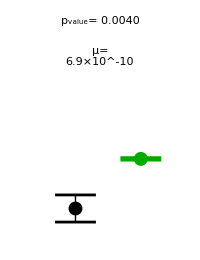

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STR_2allele_no_lag_Pregrowth.png

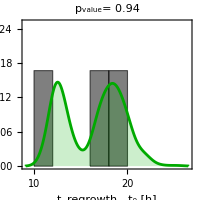

KS-test p-value: 0.940247

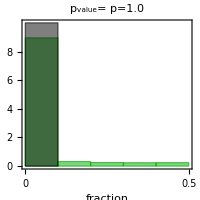

fraction below 0.1 (exp):1.

fraction below 0.1 (sim):0.895184

```mathematica
simdist=Table[Import["models\\STR\\distribution_fixed_mu_2strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["STR_2allele_no_lag_Pregrowth.png"]
RegrowtTimeDistribution["STR_2allele_no_lag_Tregrowth.png"]
LeastAbundantStrain["STR_2allele_no_lag_LBS.png"]
```

### Find the optimal μ that maximizes the p - value of the probability of regrowth

```mathematica
Clear[RunOnce0,mu]
RunOnce0[mu_]:=RunOnce[mu]=Module[{pval,simcfus,processes,tmp,simdist},
SetDirectory[NotebookDirectory[]<>"\\models\\STR"];

args=Table[
{"optimization"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],"300",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
ret=RunProcess[{"powershell",name}]; (* waits until the process exits *)

simdist=Table[Import["distribution_optimization"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
SetDirectory[NotebookDirectory[]];
pval=FisherExactTest[Length[Select[tmp,NumberQ[#1⟦2⟧]&]],Length[tmp],Length[Select[tregrowths,NumberQ[#1]&]],Length[tregrowths]];
Return[-pval]]
```

```mathematica
NaiveMinimization[RunOnce0,10^-10,5*10^-10,0.2*10^-10]
```

1.×10^-10 3.47214×10^-10 fa=-0.192771 fb=-0.118273

1.×10^-10 2.52786×10^-10 fa=-0.237245 fb=-0.192771

1.×10^-10 1.94427×10^-10 fa=-0.239736 fb=-0.237245

1.36068×10^-10 1.94427×10^-10 fa=-0.234346 fb=-0.237245

1.58359×10^-10 1.94427×10^-10 fa=-0.239736 fb=-0.237245

1.58359×10^-10 1.8065×10^-10 fa=-0.239935 fb=-0.237477

1.58359×10^-10 1.72136×10^-10 fa=-0.240931 fb=-0.239935

1.65248×10^-10

### This value seems low and very different to the fluctuation-test based value, but we shall see later it agrees with the estimate based on the mutant number distribution.

### Short - term experiment (only large colonies counted):

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
Do[
(* parent strains before and after the antibiotic *)
wt={{births2[[nn,1]],births2[[nn,1]]},{0,0}};
(* mutant strains before and after the antibiotic *)
mt=births2[[nn,1]]{{1,1},{1,1}};
Export[NotebookDirectory[]<>"\\models\\STR\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

6.9×10^-10

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\STR"]

args=Table[
{"preexist_res_2strains_1_allele_"<>mutrate<>"_STR"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STR

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 16 13 preexist_res_2strains_1_allele_6.9e-10_STR1 25.36 0.00411525 100 4.90375 100 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_1.dat  0.1 preexist_res_2strains_1_allele_6.9e-10_STR2 25.41 0.00401786 100 4.90378 100 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_2.dat  0.1 preexist_res_2strains_1_allele_6.9e-10_STR3 25.28 0.00526076 100 4.90383 100 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_3.dat  0.1 preexist_res_2strains_1_allele_6.9e-10_STR4 27.76 0.00382394 100 4.90389 100 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_4.dat  0.1 preexist_res_2strains_1_allele_6.9e-10_STR5 25.9 0.00380994 100 4.93022 100 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_5.dat  0.1 preexist_res_2strains_1_allele_6.9e-10_STR6 25.52 0.00370782 100 4.93025 100 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_6.dat  0.1 preexist_res_2strains_1_allele_6.9e-10_STR7 25.53 0.00375746 100 4.93031 100 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_7.dat  0.1 preexist_res_2strains_1_allele_6.9e-10_STR8 26.79 0.00355693 100 4.93036 100 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_8.dat  0.1 preexist_res_2strains_1_allele_6.9e-10_STR9 25.75 0.00272866 100 5.02475 100 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_9.dat  0.1 preexist_res_2strains_1_allele_6.9e-10_STR10 26.06 0.0022141 100 5.02478 100 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_10.dat  0.1 preexist_res_2strains_1_allele_6.9e-10_STR11 25.07 0.00315078 100 5.02483 100 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_11.dat  0.1 preexist_res_2strains_1_allele_6.9e-10_STR12 25.46 0.0027869 100 5.02489 100 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_12.dat  0.1 preexist_res_2strains_1_allele_6.9e-10_STR13 25.45 0.00247449 100 4.77114 100 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_13.dat  0.1 preexist_res_2strains_1_allele_6.9e-10_STR14 25.63 0.00331011 100 4.77117 100 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_14.dat  0.1 preexist_res_2strains_1_allele_6.9e-10_STR15 25.22 0.00481147 100 4.77122 100 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_15.dat  0.1 preexist_res_2strains_1_allele_6.9e-10_STR16 25.14 0.00341267 100 4.77128 100 0.05 1000 6.900000000000001e-10 6.900000000000001e-10 0.75 input_params_16.dat  0.1

0

16

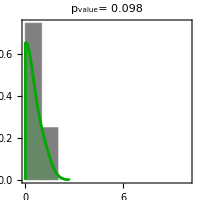

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STR_2allele_no_lag_Nmut.png

```mathematica
HistogramMutants[cfus,NotebookDirectory[]<>"\\models\\STR\\strains_preexist_res_2strains_1_allele_"<>mutrate<>"_STR",strains,alleles,NotebookDirectory[]<>"\\figures\\STR_2allele_no_lag_Nmut.png",cfubindata]
```

### Short - term experiment (all colonies large and small):

16

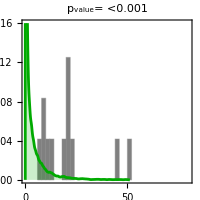

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STR_2allele_no_lag_Nmut_allcolonies.png

```mathematica
HistogramMutants[cfusall,NotebookDirectory[]<>"\\models\\STR\\strains_preexist_res_2strains_1_allele_"<>mutrate<>"_STR",strains,alleles,NotebookDirectory[]<>"\\figures\\STR_2allele_no_lag_Nmut_allcolonies.png",cfuallbindata]
```

### Find the optimal μ that maximizes the p - value when fitted to the mutant number distribution (only large colonies):

```mathematica
Clear[RunOnce,mu]
RunOnce[mu_]:=RunOnce[mu]=Module[{pval,simcfus,processes},
SetDirectory[NotebookDirectory[]<>"\\models\\STR"];

args=Table[
{"optimization"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],"100",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
ret=RunProcess[{"powershell",name}]; (* waits until the process exits *)

simcfus=Table[ReadList["strains_optimization"<>ToString[n]<>".dat",{Number,Number,Number,Number}],{n,Length[births2]}];
SetDirectory[NotebookDirectory[]];
pval=KolmogorovSmirnovTest[Flatten[Table[Table[Total[simcfus[[k,i,3;;]]],{i,Length[simcfus[[k]]]}],{k,Length[simcfus]}]],cfus];
Return[-pval]]
```

```mathematica
NaiveMinimization[RunOnce,10^-10,5*10^-10,0.2*10^-10]
```

1.×10^-10 3.47214×10^-10 fa=-0.421886 fb=-0.183227

1.×10^-10 2.52786×10^-10 fa=-0.473516 fb=-0.421886

1.×10^-10 1.94427×10^-10 fa=-0.500414 fb=-0.473516

1.36068×10^-10 1.94427×10^-10 fa=-0.459558 fb=-0.473516

1.36068×10^-10 1.72136×10^-10 fa=-0.500414 fb=-0.461355

1.49845×10^-10 1.72136×10^-10 fa=-0.479879 fb=-0.461355

1.58359×10^-10 1.72136×10^-10 fa=-0.500414 fb=-0.461355

1.65248×10^-10

#### This is comparable with μ obtained above when fitting to the regrowth probability.

### For comparison, let us find the optimal μ that maximizes the p - value for the mutant number distribution when colonies of all sizes (small and large) are included:

```mathematica
Clear[RunOnce,mu]
RunOnce[mu_]:=RunOnce[mu]=Module[{pval,simcfus,processes},
SetDirectory[NotebookDirectory[]<>"\\models\\STR"];

args=Table[
{"optimization"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],"100",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
ret=RunProcess[{"powershell",name}]; (* waits until the process exits *)

simcfus=Table[ReadList["strains_optimization"<>ToString[n]<>".dat",{Number,Number,Number,Number}],{n,Length[births2]}];
SetDirectory[NotebookDirectory[]];
pval=KolmogorovSmirnovTest[Flatten[Table[Table[Total[simcfus[[k,i,3;;]]],{i,Length[simcfus[[k]]]}],{k,Length[simcfus]}]],cfusall];
Return[-pval]]
```

```mathematica
NaiveMinimization[RunOnce,10^-9,10^-8,10^-10]
```

1.×10^-9 6.56231×10^-9 fa=-0.569175 fb=-0.0793556

3.12461×10^-9 6.56231×10^-9 fa=-0.0428008 fb=-0.0793556

3.12461×10^-9 5.24922×10^-9 fa=-0.569175 fb=-0.451659

3.93614×10^-9 5.24922×10^-9 fa=-0.333475 fb=-0.451659

4.43769×10^-9 5.24922×10^-9 fa=-0.569175 fb=-0.451659

4.43769×10^-9 4.93925×10^-9 fa=-0.794127 fb=-0.68786

4.62927×10^-9 4.93925×10^-9 fa=-0.777972 fb=-0.68786

4.62927×10^-9 4.82085×10^-9 fa=-0.794127 fb=-0.697122

4.70245×10^-9 4.82085×10^-9 fa=-0.700935 fb=-0.697122

4.70245×10^-9 4.77562×10^-9 fa=-0.794127 fb=-0.753843

4.73903×10^-9

#### This value is much too high compared to the regrowth probability-based μ. Nevertheless, we shall check how this value of μ affects other observables:

## Single allele model for STR, fitted to the P(N_mut) data (all colonies)

```mathematica
mutrate="4.7e-9";  (* NEW value from fitting the data *)
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\STR_fitted_all\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->1234]
```

4.7×10^-9

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\STR_fitted_all"]

args=Table[
{"fixed_mu_2strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STR_fitted_all

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 24 13 fixed_mu_2strains_1 25.36 0.00390997 5.02403 26.3585 22.1833 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_1.dat 0.1 fixed_mu_2strains_2 25.28 0.00306923 5.43511 26.3585 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_2.dat 0.1 fixed_mu_2strains_3 25.47 0.00454993 4.53633 26.3586 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_3.dat 0.1 fixed_mu_2strains_4 27.33 0.00358976 4.46008 26.3586 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_4.dat 0.1 fixed_mu_2strains_5 25.49 0.00366958 4.97181 24.5648 23.9676 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_5.dat 0.1 fixed_mu_2strains_6 25.31 0.00296837 5.38567 24.5648 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_6.dat 0.1 fixed_mu_2strains_7 24.44 0.0036963 4.82925 24.5649 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_7.dat 0.1 fixed_mu_2strains_8 26.93 0.00307623 4.61753 24.5649 16.4411 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_8.dat 0.1 fixed_mu_2strains_9 24.44 0.00327829 4.58783 25.384 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_9.dat 0.1 fixed_mu_2strains_10 24.96 0.00301268 5.3875 25.3841 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_10.dat 0.1 fixed_mu_2strains_11 25.62 0.00426521 5.07981 25.3841 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_11.dat 0.1 fixed_mu_2strains_12 27.1 0.00347171 4.63014 25.3842 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_12.dat 0.1 fixed_mu_2strains_13 25.6 0.00366434 4.85767 29.4525 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_13.dat 0.1 fixed_mu_2strains_14 25.04 0.00272118 5.41339 29.4525 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_14.dat 0.1 fixed_mu_2strains_15 25.29 0.00394519 5.43189 29.4525 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_15.dat 0.1 fixed_mu_2strains_16 26.72 0.00307794 4.92569 29.4528 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_16.dat 0.1 fixed_mu_2strains_17 25.94 0.0022595 5.28839 27.6709 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_17.dat 0.1 fixed_mu_2strains_18 25.41 0.00209291 5.93381 27.6709 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_18.dat 0.1 fixed_mu_2strains_19 25.04 0.0023283 5.86922 27.671 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_19.dat 0.1 fixed_mu_2strains_20 26.66 0.0022353 5.10317 27.671 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_20.dat 0.1 fixed_mu_2strains_21 26.1 0.00463298 5.41208 30.9639 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_21.dat 0.1 fixed_mu_2strains_22 25.05 0.00363034 5.46603 30.9639 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_22.dat 0.1 fixed_mu_2strains_23 25.1 0.00613354 4.73758 30.9642 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_23.dat 0.1 fixed_mu_2strains_24 26.98 0.00524312 4.55267 30.9642 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_24.dat 0.1

0

0.937252

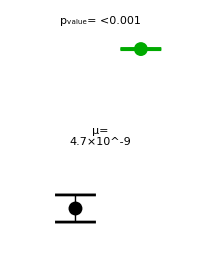

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STR_fitted_2allele_no_lag_Pregrowth_allcolonies.png

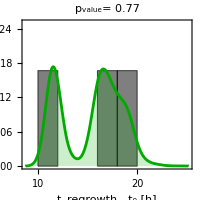

KS-test p-value: 0.767721

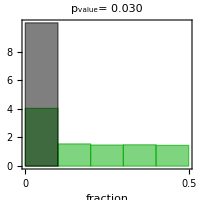

fraction below 0.1 (exp):1.

fraction below 0.1 (sim):0.403353

```mathematica
simdist=Table[Import["models\\STR_fitted_all\\distribution_fixed_mu_2strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["STR_fitted_2allele_no_lag_Pregrowth_allcolonies.png"]
RegrowtTimeDistribution["STR_fitted_2allele_no_lag_Tregrowth_allcolonies.png"]
LeastAbundantStrain["STR_fitted_2allele_no_lag_LBS_allcolonies.png"]
```

### Short - term experiment:

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
Do[
(* parent strains before and after the antibiotic *)
wt={{births2[[nn,1]],births2[[nn,1]]},{0,0}};
(* mutant strains before and after the antibiotic *)
mt=births2[[nn,1]]{{1,1},{1,1}};
Export[NotebookDirectory[]<>"\\models\\STR_fitted_all\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

4.7×10^-9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\STR_fitted_all"]

args=Table[
{"preexist_res_2strains_1_allele_"<>mutrate<>"_STR"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STR_fitted_all

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 16 13 preexist_res_2strains_1_allele_4.7e-9_STR1 25.36 0.00411525 100 4.90375 100 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_1.dat  0.1 preexist_res_2strains_1_allele_4.7e-9_STR2 25.41 0.00401786 100 4.90378 100 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_2.dat  0.1 preexist_res_2strains_1_allele_4.7e-9_STR3 25.28 0.00526076 100 4.90383 100 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_3.dat  0.1 preexist_res_2strains_1_allele_4.7e-9_STR4 27.76 0.00382394 100 4.90389 100 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_4.dat  0.1 preexist_res_2strains_1_allele_4.7e-9_STR5 25.9 0.00380994 100 4.93022 100 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_5.dat  0.1 preexist_res_2strains_1_allele_4.7e-9_STR6 25.52 0.00370782 100 4.93025 100 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_6.dat  0.1 preexist_res_2strains_1_allele_4.7e-9_STR7 25.53 0.00375746 100 4.93031 100 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_7.dat  0.1 preexist_res_2strains_1_allele_4.7e-9_STR8 26.79 0.00355693 100 4.93036 100 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_8.dat  0.1 preexist_res_2strains_1_allele_4.7e-9_STR9 25.75 0.00272866 100 5.02475 100 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_9.dat  0.1 preexist_res_2strains_1_allele_4.7e-9_STR10 26.06 0.0022141 100 5.02478 100 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_10.dat  0.1 preexist_res_2strains_1_allele_4.7e-9_STR11 25.07 0.00315078 100 5.02483 100 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_11.dat  0.1 preexist_res_2strains_1_allele_4.7e-9_STR12 25.46 0.0027869 100 5.02489 100 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_12.dat  0.1 preexist_res_2strains_1_allele_4.7e-9_STR13 25.45 0.00247449 100 4.77114 100 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_13.dat  0.1 preexist_res_2strains_1_allele_4.7e-9_STR14 25.63 0.00331011 100 4.77117 100 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_14.dat  0.1 preexist_res_2strains_1_allele_4.7e-9_STR15 25.22 0.00481147 100 4.77122 100 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_15.dat  0.1 preexist_res_2strains_1_allele_4.7e-9_STR16 25.14 0.00341267 100 4.77128 100 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_16.dat  0.1

0

16

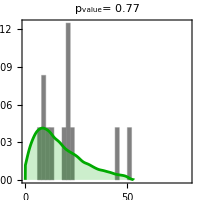

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STR_fitted_2allele_no_lag_Nmut_allcolonies.png

```mathematica
HistogramMutants[cfusall,NotebookDirectory[]<>"\\models\\STR_fitted_all\\strains_preexist_res_2strains_1_allele_"<>mutrate<>"_STR",strains,alleles,NotebookDirectory[]<>"\\figures\\STR_fitted_2allele_no_lag_Nmut_allcolonies.png",cfuallbindata]
```

## Single allele model for STR with filamentation, fitted to the P(N_mut) data (all colonies)

```mathematica
mutrate="4.7e-9";  (* NEW value from fitting the data *)
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\STR_filament_fitted_all\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","0.66",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->1234]
```

4.7×10^-9

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\STR_filament_fitted_all"]

args=Table[
{"fixed_mu_2strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STR_filament_fitted_all

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 24 13 fixed_mu_2strains_1 25.36 0.00390997 5.02403 26.3585 22.1833 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_1.dat 0.1 fixed_mu_2strains_2 25.28 0.00306923 5.43511 26.3585 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_2.dat 0.1 fixed_mu_2strains_3 25.47 0.00454993 4.53633 26.3586 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_3.dat 0.1 fixed_mu_2strains_4 27.33 0.00358976 4.46008 26.3586 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_4.dat 0.1 fixed_mu_2strains_5 25.49 0.00366958 4.97181 24.5648 23.9676 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_5.dat 0.1 fixed_mu_2strains_6 25.31 0.00296837 5.38567 24.5648 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_6.dat 0.1 fixed_mu_2strains_7 24.44 0.0036963 4.82925 24.5649 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_7.dat 0.1 fixed_mu_2strains_8 26.93 0.00307623 4.61753 24.5649 16.4411 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_8.dat 0.1 fixed_mu_2strains_9 24.44 0.00327829 4.58783 25.384 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_9.dat 0.1 fixed_mu_2strains_10 24.96 0.00301268 5.3875 25.3841 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_10.dat 0.1 fixed_mu_2strains_11 25.62 0.00426521 5.07981 25.3841 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_11.dat 0.1 fixed_mu_2strains_12 27.1 0.00347171 4.63014 25.3842 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_12.dat 0.1 fixed_mu_2strains_13 25.6 0.00366434 4.85767 29.4525 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_13.dat 0.1 fixed_mu_2strains_14 25.04 0.00272118 5.41339 29.4525 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_14.dat 0.1 fixed_mu_2strains_15 25.29 0.00394519 5.43189 29.4525 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_15.dat 0.1 fixed_mu_2strains_16 26.72 0.00307794 4.92569 29.4528 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_16.dat 0.1 fixed_mu_2strains_17 25.94 0.0022595 5.28839 27.6709 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_17.dat 0.1 fixed_mu_2strains_18 25.41 0.00209291 5.93381 27.6709 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_18.dat 0.1 fixed_mu_2strains_19 25.04 0.0023283 5.86922 27.671 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_19.dat 0.1 fixed_mu_2strains_20 26.66 0.0022353 5.10317 27.671 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_20.dat 0.1 fixed_mu_2strains_21 26.1 0.00463298 5.41208 30.9639 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_21.dat 0.1 fixed_mu_2strains_22 25.05 0.00363034 5.46603 30.9639 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_22.dat 0.1 fixed_mu_2strains_23 25.1 0.00613354 4.73758 30.9642 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_23.dat 0.1 fixed_mu_2strains_24 26.98 0.00524312 4.55267 30.9642 30 0.05 1000 4.700000000000001e-9 4.700000000000001e-9 0.75 input_params_24.dat 0.1

0

0.894096

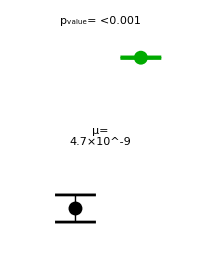

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STR_filam_fitted_all_2allele_no_lag_Pregrowth.png

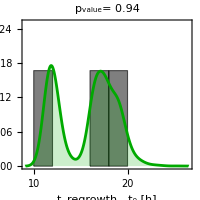

KS-test p-value: 0.944267

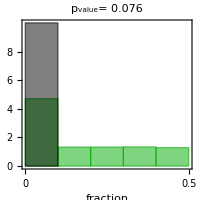

fraction below 0.1 (exp):1.

fraction below 0.1 (sim):0.470826

```mathematica
simdist=Table[Import["models\\STR_filament_fitted_all\\distribution_fixed_mu_2strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["STR_filam_fitted_all_2allele_no_lag_Pregrowth.png"]
RegrowtTimeDistribution["STR_filam_fitted_all_2allele_no_lag_Tregrowth.png"]
LeastAbundantStrain["STR_filam_fitted_2allele_all_no_lag_LBS.png"]
```

### The higher μ fitted to all colonies obviously does not reproduce the experimental regrowth probability. We therefore go back to the smaller μ = 1.6 x 10^-10, which fits better P(regrowth) and also P(N_mutants) (μ was fitted to it). The new model includes filamentation but this does not affect the distribution P(N_mutants), so no need to optimize μ again.

## Single allele model for STR with filamentation, fitted to the P(N_mut) data (only large colonies)

```mathematica
mutrate="1.6e-10";  (* NEW value from fitting the data *)
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\STR_filament_fitted\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","0.66",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->1234]
```

1.6×10^-10

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\STR_filament_fitted"]

args=Table[
{"fixed_mu_2strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STR_filament_fitted

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 24 13 fixed_mu_2strains_1 25.36 0.00390997 5.02403 26.3585 22.1833 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_1.dat 0.1 fixed_mu_2strains_2 25.28 0.00306923 5.43511 26.3585 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_2.dat 0.1 fixed_mu_2strains_3 25.47 0.00454993 4.53633 26.3586 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_3.dat 0.1 fixed_mu_2strains_4 27.33 0.00358976 4.46008 26.3586 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_4.dat 0.1 fixed_mu_2strains_5 25.49 0.00366958 4.97181 24.5648 23.9676 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_5.dat 0.1 fixed_mu_2strains_6 25.31 0.00296837 5.38567 24.5648 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_6.dat 0.1 fixed_mu_2strains_7 24.44 0.0036963 4.82925 24.5649 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_7.dat 0.1 fixed_mu_2strains_8 26.93 0.00307623 4.61753 24.5649 16.4411 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_8.dat 0.1 fixed_mu_2strains_9 24.44 0.00327829 4.58783 25.384 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_9.dat 0.1 fixed_mu_2strains_10 24.96 0.00301268 5.3875 25.3841 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_10.dat 0.1 fixed_mu_2strains_11 25.62 0.00426521 5.07981 25.3841 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_11.dat 0.1 fixed_mu_2strains_12 27.1 0.00347171 4.63014 25.3842 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_12.dat 0.1 fixed_mu_2strains_13 25.6 0.00366434 4.85767 29.4525 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_13.dat 0.1 fixed_mu_2strains_14 25.04 0.00272118 5.41339 29.4525 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_14.dat 0.1 fixed_mu_2strains_15 25.29 0.00394519 5.43189 29.4525 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_15.dat 0.1 fixed_mu_2strains_16 26.72 0.00307794 4.92569 29.4528 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_16.dat 0.1 fixed_mu_2strains_17 25.94 0.0022595 5.28839 27.6709 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_17.dat 0.1 fixed_mu_2strains_18 25.41 0.00209291 5.93381 27.6709 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_18.dat 0.1 fixed_mu_2strains_19 25.04 0.0023283 5.86922 27.671 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_19.dat 0.1 fixed_mu_2strains_20 26.66 0.0022353 5.10317 27.671 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_20.dat 0.1 fixed_mu_2strains_21 26.1 0.00463298 5.41208 30.9639 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_21.dat 0.1 fixed_mu_2strains_22 25.05 0.00363034 5.46603 30.9639 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_22.dat 0.1 fixed_mu_2strains_23 25.1 0.00613354 4.73758 30.9642 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_23.dat 0.1 fixed_mu_2strains_24 26.98 0.00524312 4.55267 30.9642 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_24.dat 0.1

0

0.086264

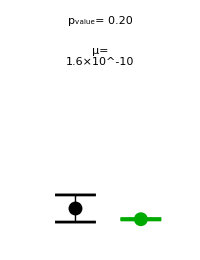

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STR_filam_fitted_2allele_no_lag_Pregrowth.png

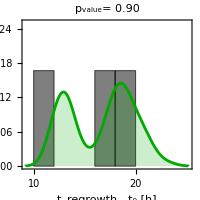

KS-test p-value: 0.900501

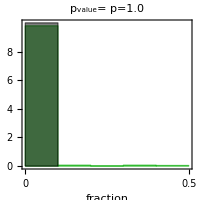

fraction below 0.1 (exp):1.

fraction below 0.1 (sim):0.979268

```mathematica
simdist=Table[Import["models\\STR_filament_fitted\\distribution_fixed_mu_2strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["STR_filam_fitted_2allele_no_lag_Pregrowth.png"]
RegrowtTimeDistribution["STR_filam_fitted_2allele_no_lag_Tregrowth.png"]
LeastAbundantStrain["STR_filam_fitted_2allele_no_lag_LBS.png"]
```

### Short - term experiment:

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
Do[
(* parent strains before and after the antibiotic *)
wt={{births2[[nn,1]],births2[[nn,1]]},{0,0}};
(* mutant strains before and after the antibiotic *)
mt=births2[[nn,1]]{{1,1},{1,1}};
Export[NotebookDirectory[]<>"\\models\\STR_filament_fitted\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","0.66",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

1.6×10^-10

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\STR_filament_fitted"]

args=Table[
{"preexist_res_2strains_1_allele_"<>mutrate<>"_STR"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STR_filament_fitted

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 16 13 preexist_res_2strains_1_allele_1.6e-10_STR1 25.36 0.00411525 100 4.90375 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_1.dat  0.1 preexist_res_2strains_1_allele_1.6e-10_STR2 25.41 0.00401786 100 4.90378 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_2.dat  0.1 preexist_res_2strains_1_allele_1.6e-10_STR3 25.28 0.00526076 100 4.90383 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_3.dat  0.1 preexist_res_2strains_1_allele_1.6e-10_STR4 27.76 0.00382394 100 4.90389 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_4.dat  0.1 preexist_res_2strains_1_allele_1.6e-10_STR5 25.9 0.00380994 100 4.93022 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_5.dat  0.1 preexist_res_2strains_1_allele_1.6e-10_STR6 25.52 0.00370782 100 4.93025 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_6.dat  0.1 preexist_res_2strains_1_allele_1.6e-10_STR7 25.53 0.00375746 100 4.93031 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_7.dat  0.1 preexist_res_2strains_1_allele_1.6e-10_STR8 26.79 0.00355693 100 4.93036 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_8.dat  0.1 preexist_res_2strains_1_allele_1.6e-10_STR9 25.75 0.00272866 100 5.02475 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_9.dat  0.1 preexist_res_2strains_1_allele_1.6e-10_STR10 26.06 0.0022141 100 5.02478 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_10.dat  0.1 preexist_res_2strains_1_allele_1.6e-10_STR11 25.07 0.00315078 100 5.02483 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_11.dat  0.1 preexist_res_2strains_1_allele_1.6e-10_STR12 25.46 0.0027869 100 5.02489 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_12.dat  0.1 preexist_res_2strains_1_allele_1.6e-10_STR13 25.45 0.00247449 100 4.77114 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_13.dat  0.1 preexist_res_2strains_1_allele_1.6e-10_STR14 25.63 0.00331011 100 4.77117 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_14.dat  0.1 preexist_res_2strains_1_allele_1.6e-10_STR15 25.22 0.00481147 100 4.77122 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_15.dat  0.1 preexist_res_2strains_1_allele_1.6e-10_STR16 25.14 0.00341267 100 4.77128 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_16.dat  0.1

0

16

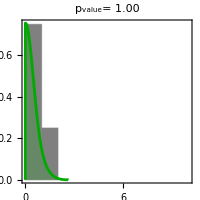

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STR_filam_fitted_2allele_no_lag_Nmut.png

```mathematica
HistogramMutants[cfus,NotebookDirectory[]<>"\\models\\STR_filament_fitted\\strains_preexist_res_2strains_1_allele_"<>mutrate<>"_STR",strains,alleles,NotebookDirectory[]<>"\\figures\\STR_filam_fitted_2allele_no_lag_Nmut.png",cfubindata]
```

## Phenotypic lag model for STR with filamentation. One resistant allele. Mixed strains AD30 and AD30YFP .

```mathematica
mutrate="1.6e-10";  (* value as in the no-lag fitted model *)
lagrate="0.5" ; (* this must be experimentally chosen to give the best fit *)
intgrfraction=0.8; (* this must be experimentally chosen to give the best fit *)
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={{births[[nn,1]],births[[nn,1]]},{0,0}};
(* intermediate strains before and after the antibiotics*)
it={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{intgrfraction,intgrfraction}}; (* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\STR_filament_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","0.66",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],{1,1},{"end"}],"Table"]  (* we use the same model as for CIP but with different parameters of the delayed response *)
,{nn,Length[vols]}],RandomSeeding->123]
```

1.6×10^-10

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\STR_filament_lag"]

args=Table[
{"fixed_mu_2strains_lag_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1",lagrate},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STR_filament_lag

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 24 14 fixed_mu_2strains_lag_1 25.36 0.00390997 5.02403 26.3585 22.1833 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_1.dat 0.1 0.5 fixed_mu_2strains_lag_2 25.28 0.00306923 5.43511 26.3585 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_2.dat 0.1 0.5 fixed_mu_2strains_lag_3 25.47 0.00454993 4.53633 26.3586 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_3.dat 0.1 0.5 fixed_mu_2strains_lag_4 27.33 0.00358976 4.46008 26.3586 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_4.dat 0.1 0.5 fixed_mu_2strains_lag_5 25.49 0.00366958 4.97181 24.5648 23.9676 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_5.dat 0.1 0.5 fixed_mu_2strains_lag_6 25.31 0.00296837 5.38567 24.5648 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_6.dat 0.1 0.5 fixed_mu_2strains_lag_7 24.44 0.0036963 4.82925 24.5649 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_7.dat 0.1 0.5 fixed_mu_2strains_lag_8 26.93 0.00307623 4.61753 24.5649 16.4411 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_8.dat 0.1 0.5 fixed_mu_2strains_lag_9 24.44 0.00327829 4.58783 25.384 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_9.dat 0.1 0.5 fixed_mu_2strains_lag_10 24.96 0.00301268 5.3875 25.3841 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_10.dat 0.1 0.5 fixed_mu_2strains_lag_11 25.62 0.00426521 5.07981 25.3841 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_11.dat 0.1 0.5 fixed_mu_2strains_lag_12 27.1 0.00347171 4.63014 25.3842 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_12.dat 0.1 0.5 fixed_mu_2strains_lag_13 25.6 0.00366434 4.85767 29.4525 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_13.dat 0.1 0.5 fixed_mu_2strains_lag_14 25.04 0.00272118 5.41339 29.4525 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_14.dat 0.1 0.5 fixed_mu_2strains_lag_15 25.29 0.00394519 5.43189 29.4525 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_15.dat 0.1 0.5 fixed_mu_2strains_lag_16 26.72 0.00307794 4.92569 29.4528 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_16.dat 0.1 0.5 fixed_mu_2strains_lag_17 25.94 0.0022595 5.28839 27.6709 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_17.dat 0.1 0.5 fixed_mu_2strains_lag_18 25.41 0.00209291 5.93381 27.6709 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_18.dat 0.1 0.5 fixed_mu_2strains_lag_19 25.04 0.0023283 5.86922 27.671 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_19.dat 0.1 0.5 fixed_mu_2strains_lag_20 26.66 0.0022353 5.10317 27.671 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_20.dat 0.1 0.5 fixed_mu_2strains_lag_21 26.1 0.00463298 5.41208 30.9639 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_21.dat 0.1 0.5 fixed_mu_2strains_lag_22 25.05 0.00363034 5.46603 30.9639 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_22.dat 0.1 0.5 fixed_mu_2strains_lag_23 25.1 0.00613354 4.73758 30.9642 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_23.dat 0.1 0.5 fixed_mu_2strains_lag_24 26.98 0.00524312 4.55267 30.9642 30 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_24.dat 0.1 0.5

0

0.0875728

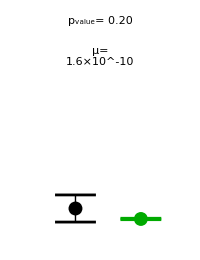

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STR_filam_2allele_lag_Pregrowth.png

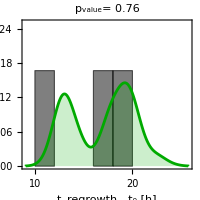

KS-test p-value: 0.76219

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STR_filam_lag_params.png

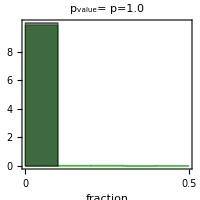

fraction below 0.1 (exp):1.

fraction below 0.1 (sim):0.982554

```mathematica
simdist=Table[Import["models\\STR_filament_lag\\distribution_fixed_mu_2strains_lag_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["STR_filam_2allele_lag_Pregrowth.png"]
RegrowtTimeDistribution["STR_filam_2allele_lag_Tregrowth.png"]
Export[NotebookDirectory[]<>"\\figures\\STR_filam_lag_params.png",Style["μ="<>mutrate<>"\nω="<>lagrate<>"\nq="<>ToString[intgrfraction],FontSize->32],"PNG",ImageSize->300]
LeastAbundantStrain["STR_filam_2allele_lag_LBS.png"]
```

### Now optimize the model with respect to both ω and q:

```mathematica
Clear[RunOnce2,ω,q]
mu=Interpreter["Number"][mutrate]
RunOnce2[ω_?NumericQ,q_?NumericQ]:=RunOnce2[ω,q]=Module[{pval1,pval2,pval3,fractions,simcfus,simdist,tmp,psurv,psurvexp,ret,processes},
(*Return[ω^2+q^2]*)
strains=2;alleles=1;
BlockRandom[Do[
wt={{births[[nn,1]],births[[nn,1]]},{0,0}};
it={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{Abs[q],Abs[q]}}; 
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};
Export[NotebookDirectory[]<>"\\models\\STR_filament_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","0.66",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],{1,1},{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->123];
SetDirectory[NotebookDirectory[]<>"\\models\\STR_filament_lag"];

args=Table[
{"optimization_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],"300",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1",ToString[Abs[ω]]},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
ret=RunProcess[{"powershell",name}]; (* waits until the process exits *)

SetDirectory[NotebookDirectory[]];
simdist=Table[Import["models\\STR_filament_lag\\distribution_optimization_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
pval2=KolmogorovSmirnovTest[Select[tmp⟦All,2⟧,NumberQ[#1]&],Select[tregrowths-ainjs,NumberQ[#1]&]];
pval1=FisherExactTest[Length[Select[tmp,NumberQ[#1⟦2⟧]&]],Length[tmp],Length[Select[tregrowths,NumberQ[#1]&]],Length[tregrowths]];
fractions=Table[Min[1.#[[7]]/(#[[10]]+#[[7]]),1.#[[10]]/(#[[10]]+#[[7]])]&/@Select[simdist[[i]],(#[[7]]+#[[10]]>0)&],{i,Length[simdist]}];
pval3=KolmogorovSmirnovTest[Round[Flatten[fractions],ksround],Round[experfractions,ksround]];
ret=-FittingFunction[pval1,pval2,pval3];
Print["ω= ",ω," q =",q, " fun=",ret];
Return[ret]
]
```

1.6×10^-10

```mathematica
fits=Table[{ω,q,RunOnce2[ω,q]},{ω,0.1,0.5,0.1},{q,0,0.8,0.2}]
```

ω= 0.1 q =0. fun=-0.0210055

ω= 0.1 q =0.2 fun=-0.0422758

ω= 0.1 q =0.4 fun=-0.0721688

ω= 0.1 q =0.6 fun=-0.131663

ω= 0.1 q =0.8 fun=-0.168809

ω= 0.2 q =0. fun=-0.0537667

ω= 0.2 q =0.2 fun=-0.0874732

ω= 0.2 q =0.4 fun=-0.126372

ω= 0.2 q =0.6 fun=-0.183939

ω= 0.2 q =0.8 fun=-0.203919

ω= 0.3 q =0. fun=-0.0926579

ω= 0.3 q =0.2 fun=-0.128579

ω= 0.3 q =0.4 fun=-0.0952314

ω= 0.3 q =0.6 fun=-0.153183

ω= 0.3 q =0.8 fun=-0.185879

ω= 0.4 q =0. fun=-0.130655

ω= 0.4 q =0.2 fun=-0.119695

ω= 0.4 q =0.4 fun=-0.180526

ω= 0.4 q =0.6 fun=-0.172993

ω= 0.4 q =0.8 fun=-0.201018

ω= 0.5 q =0. fun=-0.116916

ω= 0.5 q =0.2 fun=-0.153834

ω= 0.5 q =0.4 fun=-0.17356

ω= 0.5 q =0.6 fun=-0.150521

ω= 0.5 q =0.8 fun=-0.213996

{{{0.1,0.,-0.0210055},{0.1,0.2,-0.0422758},{0.1,0.4,-0.0721688},{0.1,0.6,-0.131663},{0.1,0.8,-0.168809}},{{0.2,0.,-0.0537667},{0.2,0.2,-0.0874732},{0.2,0.4,-0.126372},{0.2,0.6,-0.183939},{0.2,0.8,-0.203919}},{{0.3,0.,-0.0926579},{0.3,0.2,-0.128579},{0.3,0.4,-0.0952314},{0.3,0.6,-0.153183},{0.3,0.8,-0.185879}},{{0.4,0.,-0.130655},{0.4,0.2,-0.119695},{0.4,0.4,-0.180526},{0.4,0.6,-0.172993},{0.4,0.8,-0.201018}},{{0.5,0.,-0.116916},{0.5,0.2,-0.153834},{0.5,0.4,-0.17356},{0.5,0.6,-0.150521},{0.5,0.8,-0.213996}}}

```mathematica
Sort[Flatten[fits,1],(#1[[3]]<#2[[3]])&]
```

{{0.5,0.8,-0.213996},{0.2,0.8,-0.203919},{0.4,0.8,-0.201018},{0.3,0.8,-0.185879},{0.2,0.6,-0.183939},{0.4,0.4,-0.180526},{0.5,0.4,-0.17356},{0.4,0.6,-0.172993},{0.1,0.8,-0.168809},{0.5,0.2,-0.153834},{0.3,0.6,-0.153183},{0.5,0.6,-0.150521},{0.1,0.6,-0.131663},{0.4,0.,-0.130655},{0.3,0.2,-0.128579},{0.2,0.4,-0.126372},{0.4,0.2,-0.119695},{0.5,0.,-0.116916},{0.3,0.4,-0.0952314},{0.3,0.,-0.0926579},{0.2,0.2,-0.0874732},{0.1,0.4,-0.0721688},{0.2,0.,-0.0537667},{0.1,0.2,-0.0422758},{0.1,0.,-0.0210055}}

### We take the first pair as the best - fit parameters and manually input it in the simulation above

### Short - term experiment :

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
Do[
(* parent strains before and after the antibiotic *)
wt={{births2[[nn,1]],births2[[nn,1]]},{0,0}};
(* intermediate strains before and after the antibiotics*)
it=births2[[nn,1]]{{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt=births2[[nn,1]]{{1,1},{1,1}};
Export[NotebookDirectory[]<>"\\models\\STR_filament_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","0.66",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],{1,1},{"end"}],"Table"]
,{nn,Length[vols2]}]
```

1.6×10^-10

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\STR_filament_lag"]

args=Table[
{"preexist_res_2strains_1_allele_lag_"<>mutrate<>"_STR"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1",lagrate},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name];

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STR_filament_lag

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 16 14 preexist_res_2strains_1_allele_lag_1.6e-10_STR1 25.36 0.00411525 100 4.90375 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_1.dat  0.1 0.5 preexist_res_2strains_1_allele_lag_1.6e-10_STR2 25.41 0.00401786 100 4.90378 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_2.dat  0.1 0.5 preexist_res_2strains_1_allele_lag_1.6e-10_STR3 25.28 0.00526076 100 4.90383 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_3.dat  0.1 0.5 preexist_res_2strains_1_allele_lag_1.6e-10_STR4 27.76 0.00382394 100 4.90389 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_4.dat  0.1 0.5 preexist_res_2strains_1_allele_lag_1.6e-10_STR5 25.9 0.00380994 100 4.93022 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_5.dat  0.1 0.5 preexist_res_2strains_1_allele_lag_1.6e-10_STR6 25.52 0.00370782 100 4.93025 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_6.dat  0.1 0.5 preexist_res_2strains_1_allele_lag_1.6e-10_STR7 25.53 0.00375746 100 4.93031 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_7.dat  0.1 0.5 preexist_res_2strains_1_allele_lag_1.6e-10_STR8 26.79 0.00355693 100 4.93036 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_8.dat  0.1 0.5 preexist_res_2strains_1_allele_lag_1.6e-10_STR9 25.75 0.00272866 100 5.02475 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_9.dat  0.1 0.5 preexist_res_2strains_1_allele_lag_1.6e-10_STR10 26.06 0.0022141 100 5.02478 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_10.dat  0.1 0.5 preexist_res_2strains_1_allele_lag_1.6e-10_STR11 25.07 0.00315078 100 5.02483 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_11.dat  0.1 0.5 preexist_res_2strains_1_allele_lag_1.6e-10_STR12 25.46 0.0027869 100 5.02489 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_12.dat  0.1 0.5 preexist_res_2strains_1_allele_lag_1.6e-10_STR13 25.45 0.00247449 100 4.77114 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_13.dat  0.1 0.5 preexist_res_2strains_1_allele_lag_1.6e-10_STR14 25.63 0.00331011 100 4.77117 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_14.dat  0.1 0.5 preexist_res_2strains_1_allele_lag_1.6e-10_STR15 25.22 0.00481147 100 4.77122 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_15.dat  0.1 0.5 preexist_res_2strains_1_allele_lag_1.6e-10_STR16 25.14 0.00341267 100 4.77128 100 0.05 1000 1.6000000000000002e-10 1.6000000000000002e-10 0.75 input_params_16.dat  0.1 0.5

16

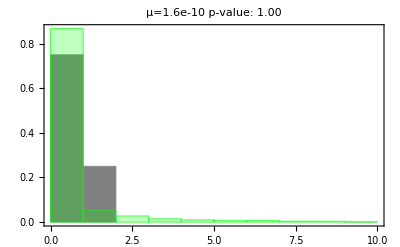

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STR_2allele_filam_lag_Nmut.png

```mathematica
simcfus=Table[ReadList[NotebookDirectory[]<>"\\models\\STR_filament_lag\\strains_preexist_res_2strains_1_allele_lag_"<>mutrate<>"_STR"<>ToString[n]<>".dat",{Number,Number,Number,Number,Number,Number}],{n,Length[births2]}];
Print[Length[simcfus]];
Show[{Histogram[cfus,{0,10,1},"PDF",ChartStyle->Gray],Histogram[Flatten[Table[Table[Total[simcfus[[k,i,3;;]]],{i,Length[simcfus[[k]]]}],{k,Length[simcfus]}]],{0,10,1},"PDF",ChartStyle->RGBColor[{0,1,0,0.25}],Frame->True,FrameLabel->{"n_r","PDF"},ImageSize->{Automatic,300},AspectRatio->0.7]},BaseStyle->FontSize->22,PlotLabel->("μ="<>mutrate<>" p-value: "<>DispPval[KolmogorovSmirnovTest[Flatten[Table[Table[Total[simcfus[[k,i,3;;]]],{i,Length[simcfus[[k]]]}],{k,Length[simcfus]}]],cfus]])]
Export[NotebookDirectory[]<>"\\figures\\STR_2allele_filam_lag_Nmut.png",%,"PNG"]
```